# Podstawowe operacje matematyczne

```mathematica
1+2
```

3

```mathematica
2^3
```

8

```mathematica
√25
```

5

```mathematica
2(1/2+3/4)
```

5/2

```mathematica
N[2/3,100]
```

0.6666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666666667

```mathematica
% 3
```

2.

```mathematica
Sin[π]
```

0

```mathematica
Sin[90 Degree]
```

1

```mathematica
Sqrt[-1]
```

ⅈ

```mathematica
a=5;
b=12;
```

```mathematica
a+b
```

17

```mathematica
3b-2a
```

26

# Funkcje

```mathematica
Abs[-2] (*Funkcje wbudowane zaczynają się od wielkiej litery*)
```

2

2

```mathematica
Tan[π/3]
```

√3

```mathematica
f[x_]:=x^2-2
```

```mathematica
f[1]
```

-1

```mathematica
g[x_,y_]:=2 x^2-3 y^2
```

```mathematica
g[1,2]
```

-10

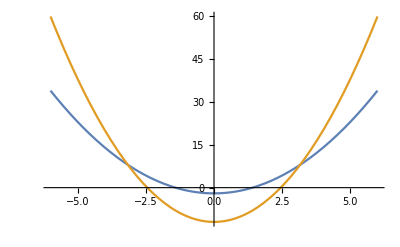

```mathematica
Plot[{f[x],g[x,2]},{x,-6,6}]
```

```mathematica
D[f[x],x] (*Pierwsza pochodna*)
```

2 x

```mathematica
D[f[x],{x,2}] (*Druga pochodna*)
```

2

```mathematica
D[g[x,y],x] (*pochodne cząstkowe*)
```

4 x

```mathematica
D[g[x,y],y]
```

-6 y

```mathematica
Integrate[f[x],x] (*całka nieoznaczona*)
```

-2 x+x^3/3

```mathematica
Integrate[g[x,y],x]
```

(2 x^3)/3-3 x y^2

```mathematica
Integrate[f[x],{x,-1,1}] (*całka oznaczona*)
```

-10/3

# Obliczenia Symboliczne

```mathematica
sol = Solve[x^2+2x-3==0,x]
```

{{x→-3},{x→1}}

```mathematica
Flatten[Values[sol]]
```

{-3,1}

```mathematica
Expand[(a+b)^5]
```

a^5+5 a^4 b+10 a^3 b^2+10 a^2 b^3+5 a b^4+b^5

```mathematica
Factor[6+11x+6 x^2+x^3]
```

(1+x) (2+x) (3+x)

```mathematica
Solve[Sin[x]==(√2)/2,x]
```

{{x→ConditionalExpression[π/4+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(3 π)/4+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[D[f[x],x]==0]
```

{{x→0}}

```mathematica
Minimize[f[x],x]
```

{-2,{x→0}}

```mathematica
approx=Series[Cos[x],{x,0,4}] (*Szereg Taylora*)
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
Normal[approx]
```

1-x^2/2+x^4/24

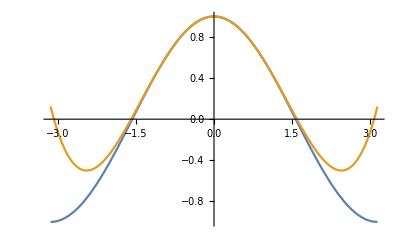

```mathematica
Plot[{Cos[x],Evaluate[Normal[approx]]},{x,-π,π}]
```

```mathematica
Sin[x]/x/.x->0
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Sum[1/n^2,{n,1,∞}]
```

π^2/6

# Badanie przebiegu zmienności funkcji

```mathematica
f[x_]:=x^3/(1-x^2)
```

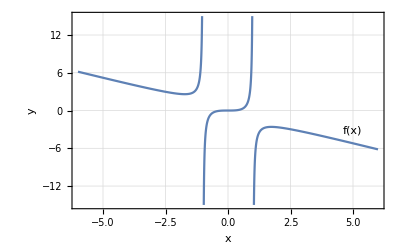

```mathematica
plot=Plot[f[x],{x,-6,6},Exclusions->{-1,1},Frame->True,GridLines->Automatic,PlotRange->{{-6,6},{-15,15}},PlotLegends->Placed["f(x)",{0.9,0.4}],FrameLabel->{"x","y"}]
```

```mathematica
zeros = {x,f(x)}/.Solve[f[x]==0,Reals]
```

{{0,0},{0,0},{0,0}}

```mathematica
extrema = {x,f[x]}/.Solve[D[f[x],x]==0&&D[f[x],{x,2}]!=0,x]
```

{{-√3,(3 √3)/2},{√3,-(3 √3)/2}}

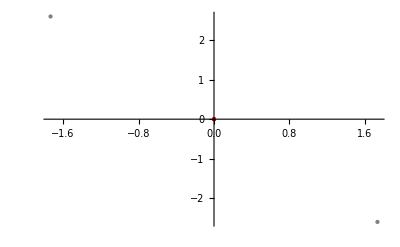

```mathematica
points =ListPlot[{zeros,extrema},PlotStyle->{{Red,PointSize[Large]},{Gray,PointSize[Large]}}]
```

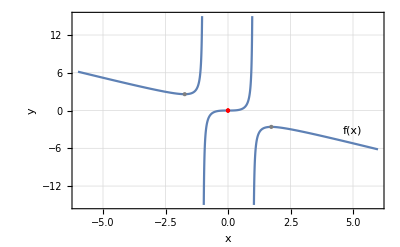

```mathematica
Show[plot,points]
```

```mathematica
Limit[f[x],x->∞]
Limit[f[x],x->-∞]
Limit[f[x],x->-1,Direction->"FromAbove"]
Limit[f[x],x->-1,Direction->"FromBelow"]
```

-∞

∞

-∞

∞

```mathematica
a=Limit[f[x]/x,x->∞];
b=Limit[f[x]-a x,x->∞];
```

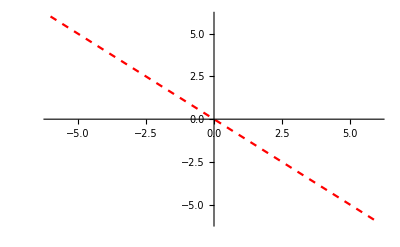

```mathematica
asym = Plot[a x + b,{x,-6,6},PlotStyle->{Red,Dashed}]
```

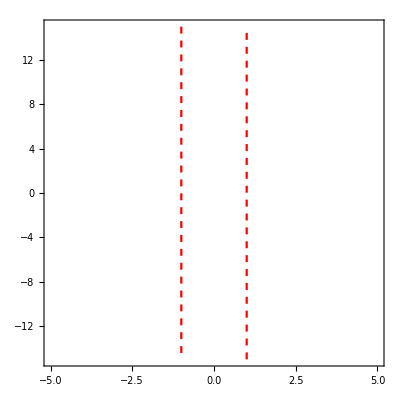

```mathematica
asym2 =ContourPlot[{x==1,x==-1},{x,-5,5},{y,-15,15},ContourStyle->{{Red, Dashed}}]
```

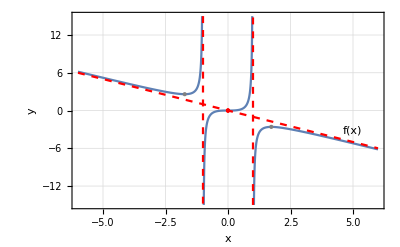

```mathematica
Show[plot,points,asym, asym2]
```

```mathematica
Clear[a,b]
```